```mathematica
(******************************************)

(* Purpose: *)
(* 1) Perform polar Fourier transformation remove translation and rotation  *)
(* 2) Output the non-normalized and normalized contours *)
(* 3) Evaluation the shape variability (S_2) for the normalized contours *)
(* NOTE: Need to run ContourAnalysis.nb first!!! *)

(* author: Chun-Biu Li *)
(* Supplemental Information of the paper:   *)
(* Variable cell growth yields reproducible organ development through spatiotemporal averaging  *)

(* Hong et al. Dev Cell 2016 *)

(******************************************)



MaxHarmonic=20; (* the max harmonics to be included *)


(*List of non-convex contour (not to used) *)
(* NonconvexList = {{mutant,sepal type,contour index},...} *)
NonconvexList={};


Do[  (* loop over mutants *)

Print[MutantName[ntempm],"---------->"];
Do[  (* loop over sepal type *)

Print[SepalType[ntemps],"........"];

(* declare variable to store Fourier coefficients *)
(* RadialFT[i,j]={{r0,Abarn[1],Bbarn[1],...,Abar[MaxHarmonic],Bbar[MaxHarmonic]},...} *)
(* norRadialFT[i,j]={{1,Abarn[1]/r0,Bbarn[1]/r0,...,Abar[MaxHarmonic]/r0,Bbar[MaxHarmonic]/r0},...} *)
(* i = 1, ... , NMutant specifies which mutant *)
(* j = 1, 2, 3 for abaxial, adaxial and lateral, respectively *)
RadialFT[ntempm,ntemps]={};
norRadialFT[ntempm,ntemps]={};  (* normalized RadialFT for mean r *)


Do[  (* loop over good contours *)


(* the contour to analyzed *)
contourtemp=Contourlist[ntempm,ntemps,1][[ntemp3]];


(* Clear up some variables *)
Clear[dt,t,tTotal];Clear[xc,yc,rp,r0];Clear[An,Bn,Cn,phi2];Clear[Abarn,Bbarn,Cbarn];


(* Find xc and yc, center of mass of contour points *)
xc=Mean[Table[contourtemp[[ntemp]][[1]],{ntemp,1,NContourPoint}]];
yc=Mean[Table[contourtemp[[ntemp]][[2]],{ntemp,1,NContourPoint}]];


(* Find r_p *)
Do[
rp[ntemp]=Sqrt[(contourtemp[[ntemp]][[1]]-xc)^2.+(contourtemp[[ntemp]][[2]]-yc)^2.];
,{ntemp,1,NContourPoint}];


(* Find Dt and t, last data point is angle zero *)
(* cross product between position vectors at NContourPoint and 1st point (with signs) *)
ctemp=Cross[{contourtemp[[NContourPoint]][[1]]-xc,contourtemp[[NContourPoint]][[2]]-yc,0.},{contourtemp[[1]][[1]]-xc,contourtemp[[1]][[2]]-yc,0.}];
atemp=ArcSin[ctemp[[3]]/(rp[NContourPoint]*rp[1])];  (* angle between the position vectors *)
dt[1]=atemp;
t[1]=atemp;

Do[
(* cross product between position vectors at ntemp-1 and ntemp th point *)
ctemp=Cross[{contourtemp[[ntemp-1]][[1]]-xc,contourtemp[[ntemp-1]][[2]]-yc,0.},{contourtemp[[ntemp]][[1]]-xc,contourtemp[[ntemp]][[2]]-yc,0.}];
atemp=ArcSin[ctemp[[3]]/(rp[ntemp-1]*rp[ntemp])];  (* angle between the position vectors *)
dt[ntemp]=Abs[atemp];  (* note only abs value is taken *)
t[ntemp]=t[ntemp-1]+dt[ntemp];
,{ntemp,2,NContourPoint}];


(* Total angle of the contour *)
tTotal=t[NContourPoint];


(* Check for convexity of the contour *)
(* If |tTotal-2*Pi| > 0.01*(2*Pi), declare non-convexity *)
ConvexFlag=1;
If[Abs[tTotal-2*Pi]>0.01*(2*Pi),
ConvexFlag=0;
NonconvexList=Append[NonconvexList,{ntempm,ntemps,ntemp3}];
];


(* Find r0 *)
r0=0.5*(rp[1]+rp[NContourPoint])*dt[1]/tTotal+0.5*Sum[(rp[ntemp]+rp[ntemp-1])*dt[ntemp],{ntemp,2,NContourPoint}]/tTotal;


(* Find a_n and b_n *)
Do[
An[ntempc]=((tTotal/(2.*ntempc*Pi))*((rp[1]-rp[NContourPoint])/dt[1])*(Cos[2.*ntempc*Pi*t[1]/tTotal]-1.)+rp[1]*Sin[2.*ntempc*Pi*t[1]/tTotal])/(Pi*ntempc); (* the ntemp = 1 term *)
Bn[ntempc]=
((tTotal/(2.*ntempc*Pi))*((rp[1]-rp[NContourPoint])/dt[1])*Sin[2.*ntempc*Pi*t[1]/tTotal]-rp[1]*Cos[2.*ntempc*Pi*t[1]/tTotal]+rp[NContourPoint])/(Pi*ntempc); (* the ntemp = 1 term *)
Atemp=0.;Btemp=0.;
Do[
(* define some valuable for faster computation *)
drtemp=(rp[ntemp]-rp[ntemp-1])/dt[ntemp];
ttemp1=2.*ntempc*Pi*t[ntemp]/tTotal;
ttemp2=2.*ntempc*Pi*t[ntemp-1]/tTotal;
ctemp=tTotal/(2.*ntempc*Pi);
Atemp=Atemp+ctemp*drtemp*(Cos[ttemp1]-Cos[ttemp2])+rp[ntemp]*Sin[ttemp1]-rp[ntemp-1]*Sin[ttemp2];
Btemp=Btemp+ctemp*drtemp*(Sin[ttemp1]-Sin[ttemp2])-rp[ntemp]*Cos[ttemp1]+rp[ntemp-1]*Cos[ttemp2];
,{ntemp,2,NContourPoint}];
Atemp=Atemp/(Pi*ntempc);
Btemp=Btemp/(Pi*ntempc);
An[ntempc]=An[ntempc]+Atemp;
Bn[ntempc]=Bn[ntempc]+Btemp;
,{ntempc,1,MaxHarmonic}];


(* Find c_n (with c_n ≥ 0) *)
Do[
Cn[ntempc]=Sqrt[An[ntempc]^2.+Bn[ntempc]^2.];
,{ntempc,1,MaxHarmonic}];


(*** !!! This part is only for Sepal contour !!! ***)
(* Find phi_2: the angle shift in the 2nd harmonic *)
phi2=Sign[Bn[2]]*Abs[ArcCos[An[2]/Cn[2]]/2.];
If[Abs[phi2]>(0.5*Pi),Print["Warning: Angle shift bigger than Pi/2!"]]; (* jusk checking *)
(*** !!! This part is only for Sepal contour !!! ***)


(* Find a^bar_n, b^bar_n and c^bar_n*)
Do[
Abarn[ntempc]=Chop[(An[ntempc]*Cos[ntempc*phi2])+(Bn[ntempc]*Sin[ntempc*phi2])];
Bbarn[ntempc]=Chop[(Bn[ntempc]*Cos[ntempc*phi2])-(An[ntempc]*Sin[ntempc*phi2])];
Cbarn[ntempc]=Sqrt[Abarn[ntempc]^2.+Bbarn[ntempc]^2.];
,{ntempc,1,MaxHarmonic}];
If[Bbarn[2]≠0.,Print["Error: Bbarn[2] ≠ 0!"];];


(********* Store the results for convex contours *********)
(* RadialFT[i,j]={{r0,Abarn[1],Bbarn[1],Abarn[2],Bbarn[2],Abarn[3],Bbarn[3]...,Abarn[MaxHarmonic],Bbarn[MaxHarmonic]},...} *)
(* norRadialFT[i,j]={{1,Abarn[1]/r0,Bbarn[1]/r0,Abarn[2]/r0,Bbarn[2]/r0,Abarn[3]/r0,Bbarn[3]/r0...,Abarn[MaxHarmonic]/r0,Bbarn[MaxHarmonic]/r0},...} *)
(* i = 1, ... , NMutant specifies which mutant *)
(* j = 1, 2, 3 for abaxial, adaxial and lateral, respectively *)
If[ConvexFlag==1, (* only store the result if the contour is nonconvex *)
ltemp={r0};
Do[
ltemp=Append[ltemp,Abarn[ntempc]];
ltemp=Append[ltemp,Bbarn[ntempc]];
,{ntempc,1,MaxHarmonic}];
RadialFT[ntempm,ntemps]=Append[RadialFT[ntempm,ntemps],ltemp];
Clear[ltemp];
];

If[ConvexFlag==1, (* only store the result if the contour is nonconvex *)
ltemp={1.};
Do[
ltemp=Append[ltemp,Abarn[ntempc]/r0];
ltemp=Append[ltemp,Bbarn[ntempc]/r0];
,{ntempc,1,MaxHarmonic}];
norRadialFT[ntempm,ntemps]=Append[norRadialFT[ntempm,ntemps],ltemp];
Clear[ltemp];
];


(* Checking Plots (can be commented out) *)
(*
Print["Blue: Data;  Red: Fourier"];
Print[Show[
ListPlot[Table[{t[ntemp]/tTotal,rp[ntemp]},{ntemp,1,NContourPoint}],PlotRange->All,Joined->True],Plot[Last[RadialFT[ntempm,ntemps]][[1]],{x,0,1},PlotStyle->Black],ListPlot[Table[{t[ntemp]/tTotal,Last[RadialFT[ntempm,ntemps]][[1]]+Sum[Last[RadialFT[ntempm,ntemps]][[2*ntempc]]*Cos[ntempc*(2*Pi*t[ntemp]/tTotal)]+Last[RadialFT[ntempm,ntemps]][[2*ntempc+1]]*Sin[ntempc*(2*Pi*t[ntemp]/tTotal)],{ntempc,1,MaxHarmonic}]},{ntemp,1,NContourPoint}],PlotStyle ->{Red,PointSize[Tiny]},Joined->False]
]];
Print[Show[
ListPolarPlot[Table[{2*Pi*t[ntemp]/tTotal,rp[ntemp]},{ntemp,1,NContourPoint}],PlotRange->All,Joined->True],PolarPlot[Last[RadialFT[ntempm,ntemps]][[1]],{x,0,2*Pi},PlotStyle->Black],ListPolarPlot[Table[{2*Pi*t[ntemp]/tTotal,Last[RadialFT[ntempm,ntemps]][[1]]+Sum[Last[RadialFT[ntempm,ntemps]][[2*ntempc]]*Cos[ntempc*(2*Pi*t[ntemp]/tTotal)]+Last[RadialFT[ntempm,ntemps]][[2*ntempc+1]]*Sin[ntempc*(2*Pi*t[ntemp]/tTotal)],{ntempc,1,MaxHarmonic}]},{ntemp,1,NContourPoint}],PlotStyle ->{Red,PointSize[Tiny]},Joined->False]]];
*)


,{ntemp3,1,Length[Filelist[ntempm,ntemps,1]]}];
,{ntemps,1,3}];  (* loop over sepal type *)
,{ntempm,1,NMutant}];  (* loop over mutants *)

Print[" "];
Print["List of nonconvex contours not to be used: ",NonconvexList];
Print["Number of abaxial contours: ",Dimensions[RadialFT[1,1]][[1]]];
Print["Number of adaxial contours: ",Dimensions[RadialFT[1,2]][[1]]];
Print["Number of lateral contours: ",Dimensions[RadialFT[1,3]][[1]]];
```

/Data_Cornell_2015_05/Col_new---------->

/aba........

/ada........

/lat........

List of nonconvex contours not to be used: {}

Number of abaxial contours: 53

Number of adaxial contours: 54

Number of lateral contours: 108

Blue: Data;  Red: Fourier

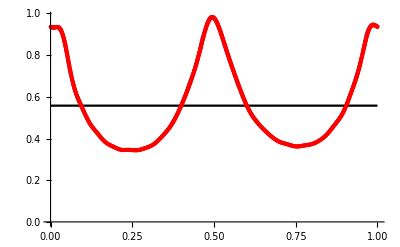

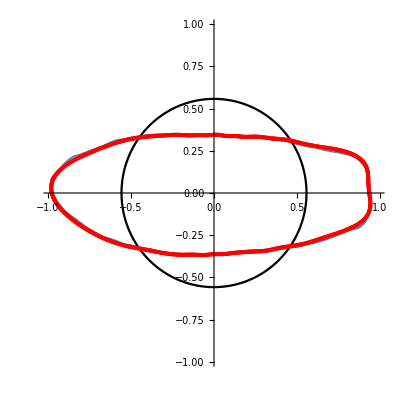

```mathematica
(* FOR CHECKING ONLY *)
(* Contour plot with alignment of the 2nd harmonics *)
Print["Blue: Data;  Red: Fourier"];
Print[Show[
ListPlot[Table[{t[ntemp]/tTotal,rp[ntemp]},{ntemp,1,NContourPoint}],PlotRange->All,Joined->True],Plot[r0,{x,0,1},PlotStyle->Black],ListPlot[Table[{t[ntemp]/tTotal,r0+Sum[Abarn[ntempc]*Cos[ntempc*(2*Pi*t[ntemp]/tTotal)]+Bbarn[ntempc]*Sin[ntempc*(2*Pi*t[ntemp]/tTotal)],{ntempc,1,MaxHarmonic}]},{ntemp,1,NContourPoint}],PlotStyle ->{Red,PointSize[Tiny]},Joined->False]
]];
Print[Show[
ListPolarPlot[Table[{2*Pi*t[ntemp]/tTotal,rp[ntemp]},{ntemp,1,NContourPoint}],PlotRange->All,Joined->True],PolarPlot[r0,{x,0,2*Pi},PlotStyle->Black],ListPolarPlot[Table[{2*Pi*t[ntemp]/tTotal,r0+Sum[Abarn[ntempc]*Cos[ntempc*(2*Pi*t[ntemp]/tTotal)]+Bbarn[ntempc]*Sin[ntempc*(2*Pi*t[ntemp]/tTotal)],{ntempc,1,MaxHarmonic}]},{ntemp,1,NContourPoint}],PlotStyle ->{Red,PointSize[Tiny]},Joined->False]]];
```

Blue: Data;  Red: Fourier

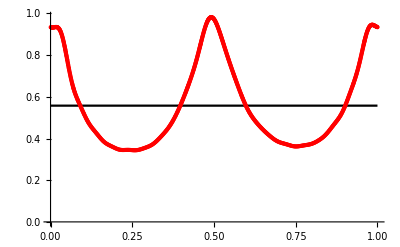

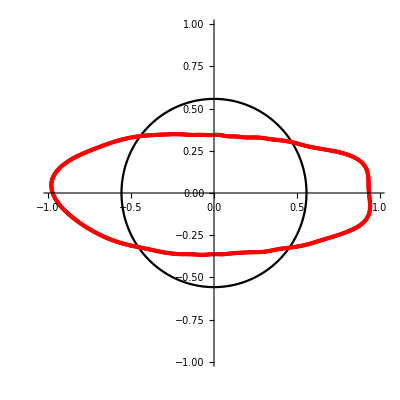

```mathematica
(* FOR CHECKING ONLY *)
(* Contour plot without alignment of the 2nd harmonics *)
Print["Blue: Data;  Red: Fourier"];
Print[Show[
ListPlot[Table[{t[ntemp]/tTotal,rp[ntemp]},{ntemp,1,NContourPoint}],PlotRange->All,Joined->True],Plot[r0,{x,0,1},PlotStyle->Black],ListPlot[Table[{t[ntemp]/tTotal,r0+Sum[An[ntempc]*Cos[ntempc*(2*Pi*t[ntemp]/tTotal)]+Bn[ntempc]*Sin[ntempc*(2*Pi*t[ntemp]/tTotal)],{ntempc,1,MaxHarmonic}]},{ntemp,1,NContourPoint}],PlotStyle ->{Red,PointSize[Tiny]},Joined->False]
]];
Print[Show[
ListPolarPlot[Table[{2*Pi*t[ntemp]/tTotal,rp[ntemp]},{ntemp,1,NContourPoint}],PlotRange->All,Joined->True],PolarPlot[r0,{x,0,2*Pi},PlotStyle->Black],ListPolarPlot[Table[{2*Pi*t[ntemp]/tTotal,r0+Sum[An[ntempc]*Cos[ntempc*(2*Pi*t[ntemp]/tTotal)]+Bn[ntempc]*Sin[ntempc*(2*Pi*t[ntemp]/tTotal)],{ntempc,1,MaxHarmonic}]},{ntemp,1,NContourPoint}],PlotStyle ->{Red,PointSize[Tiny]},Joined->False]]];
```

```mathematica
(***** Plotting for non-normalized Radial FT ******)

(* Each non-normalized contour *)
Plottempa={};
Do[ (* loop over mutant *)
Do[  (* loop over sepal type *)
Do[  (* loop over contours *)
atemp=PolarPlot[RadialFT[ntempm,ntemps][[ntemp3]][[1]]+Sum[RadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc]]*Cos[ntempc*x]+RadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc+1]]*Sin[ntempc*x],{ntempc,1,MaxHarmonic}],{x,0.,2.*Pi},PlotStyle ->{Gray,Thin}];
Plottempa=Append[Plottempa,atemp];
,{ntemp3,1,Dimensions[RadialFT[ntempm,ntemps]][[1]]}];
,{ntemps,1,3}];  (* loop over sepal type *)
,{ntempm,1,NMutant}];  (* loop over mutants *)

(* Outout the plot *)
Print[Show[Plottempa,PlotRange->{{-1.3,1.3},{-0.45,0.45}},Frame->True]];

Clear[Plottempa,atemp];
```

-Graphics-

-Graphics-

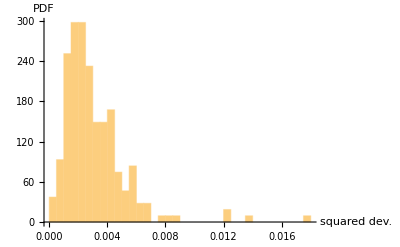

Median of squared dev.: 0.00252769

Lower and upper quantile of squared dev.: {0.00175739,0.00399278}

Lower and upper range of squared dev.: {0.000332558,0.0178725}

```mathematica
(***** Plotting for normalized Radial FT ******)
 
(* Find the median contour from norRadialFT *)

MediannorRadialFT={1.};
Do[ (* loop over Fourier components *)

atemp={};
btemp={};
Do[ (* loop over mutant *)
Do[  (* loop over sepal type *)
Do[  (* loop over contours *)
atemp=Append[atemp,norRadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc]]];
btemp=Append[btemp,norRadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc+1]]];
,{ntemp3,1,Dimensions[norRadialFT[ntempm,ntemps]][[1]]}];
,{ntemps,1,3}];  (* loop over sepal type *)
,{ntempm,1,NMutant}];  (* loop over mutants *)
MediannorRadialFT=Append[MediannorRadialFT,Median[atemp]];
MediannorRadialFT=Append[MediannorRadialFT,Median[btemp]];

,{ntempc,1,MaxHarmonic}];



(* Plotting *)

(* The median contour *)
atempm=PolarPlot[MediannorRadialFT[[1]]+Sum[MediannorRadialFT[[2*ntempc]]*Cos[ntempc*x]+MediannorRadialFT[[2*ntempc+1]]*Sin[ntempc*x],{ntempc,1,MaxHarmonic}],{x,0.,2.*Pi},PlotStyle ->Red];

(* Each normalized contour *)
Plottempa={};
Do[ (* loop over mutant *)
Do[  (* loop over sepal type *)
Do[  (* loop over contours *)
atemp=PolarPlot[norRadialFT[ntempm,ntemps][[ntemp3]][[1]]+Sum[norRadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc]]*Cos[ntempc*x]+norRadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc+1]]*Sin[ntempc*x],{ntempc,1,MaxHarmonic}],{x,0.,2.*Pi},PlotStyle ->{Gray,Thin}];
Plottempa=Append[Plottempa,atemp];
,{ntemp3,1,Dimensions[norRadialFT[ntempm,ntemps]][[1]]}];
,{ntemps,1,3}];  (* loop over sepal type *)
,{ntempm,1,NMutant}];  (* loop over mutants *)


(* Outout the plot *)
Print[Show[Plottempa,atempm,PlotRange->{{-2.7,2.7},{-0.9,0.9}},Frame->True]];

Clear[Plottempa,atemp,atempm];



(* evaluation the distribution of Mean Squared Deviation from the median contour *)

SDList={};
Do[ (* loop over mutant *)
Do[  (* loop over sepal type *)
Do[  (* loop over contours *)

stemp=0.5*Sum[(norRadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc]]-MediannorRadialFT[[2*ntempc]])^2.+(norRadialFT[ntempm,ntemps][[ntemp3]][[2*ntempc+1]]-MediannorRadialFT[[2*ntempc+1]])^2.,{ntempc,1,MaxHarmonic}];
SDList=Append[SDList,stemp];

,{ntemp3,1,Dimensions[norRadialFT[ntempm,ntemps]][[1]]}];
,{ntemps,1,3}];  (* loop over sepal type *)
,{ntempm,1,NMutant}];  (* loop over mutants *)

Print[Histogram[SDList,25,"PDF",PlotRange->All,AxesLabel->{"squared dev.","PDF"}]];
Print["Median of squared dev.: ",Median[SDList]];
Print["Lower and upper quantile of squared dev.: ",Quantile[SDList,{1/4,3/4}]];
Print["Lower and upper range of squared dev.: ",Quantile[SDList,{0.,1.}]];
```

```mathematica
Print["List of SD: ",SDList];
Export["/Users/dilaton/Documents/Komatsuzaki_temp/HFSP_PlantCell/Data_SepalShape/PolarFT/Analysis_ftsh4paper/Col_Cornell201505.xls",SDList,"XLS"];
```

List of SD: {0.0032583,0.00556245,0.00262507,0.00275903,0.00217117,0.00167357,0.0021347,0.00145963,0.00244792,0.00161665,0.00237497,0.00227404,0.000367491,0.00197097,0.001961,0.00116848,0.000332558,0.00579055,0.00563063,0.00363322,0.00228133,0.000474053,0.00338976,0.00146261,0.000458982,0.00249692,0.000508742,0.0124438,0.00435919,0.00124769,0.000735236,0.00056588,0.00342856,0.00200501,0.00189405,0.00198915,0.00154252,0.00318148,0.00233792,0.00175739,0.00229913,0.0062104,0.00403437,0.00420011,0.00087045,0.000992903,0.00187387,0.00272061,0.00352927,0.00400948,0.00138543,0.00474472,0.00553647,0.00300849,0.00378838,0.0067393,0.00182402,0.00194809,0.00157953,0.00130218,0.000805593,0.00372595,0.00183408,0.00225243,0.00145653,0.00284776,0.00205777,0.00388179,0.00177945,0.00142008,0.00369461,0.00118996,0.00249752,0.00108396,0.000889507,0.00410489,0.0014154,0.00276564,0.00103827,0.001266,0.00278722,0.00804639,0.00246968,0.00122112,0.0016045,0.00144606,0.00141644,0.00158175,0.00660551,0.00359518,0.00317177,0.00124496,0.00207422,0.00234071,0.00211543,0.00100533,0.00252372,0.00284816,0.00334721,0.00116574,0.00155606,0.00188385,0.00419266,0.00193488,0.00165657,0.00236448,0.00278751,0.00183125,0.00329817,0.00206627,0.00475047,0.00106694,0.00175585,0.00487097,0.00161544,0.00386565,0.00250279,0.00402777,0.00249537,0.00431474,0.00293234,0.00363476,0.0124986,0.00350271,0.00107377,0.00223165,0.00126285,0.00428002,0.00266798,0.00258316,0.00395849,0.00300018,0.00509093,0.00146222,0.00246659,0.00273924,0.00204787,0.00269083,0.00463956,0.00386305,0.00508296,0.00276136,0.0029063,0.00559097,0.00380006,0.00452994,0.00196655,0.00371145,0.00305623,0.00566818,0.00364126,0.00624982,0.000821664,0.00307973,0.0056689,0.00106799,0.00541958,0.00262521,0.00753522,0.00425212,0.00229723,0.00101568,0.0086107,0.0178725,0.0055774,0.00465742,0.00208988,0.00202531,0.00521986,0.00406447,0.00198216,0.00457001,0.00324789,0.00252769,0.00692601,0.00202087,0.00165518,0.00297435,0.00113575,0.00411273,0.00615797,0.00429628,0.00490409,0.00118961,0.00297789,0.00421811,0.000923754,0.00185507,0.00293578,0.00418048,0.00190625,0.00311044,0.00212719,0.00298923,0.0136236,0.00177596,0.00263919,0.00530165,0.0021758,0.00399278,0.00245139,0.00318089,0.00280119,0.00163519,0.00213066,0.00595802,0.000848979,0.00431041,0.00306309,0.00189941,0.00185371,0.0032653,0.00214222,0.00439532,0.00400933}